--- Initializing Visualization Engine ---

--- Generating ACH MatrixPlot ---

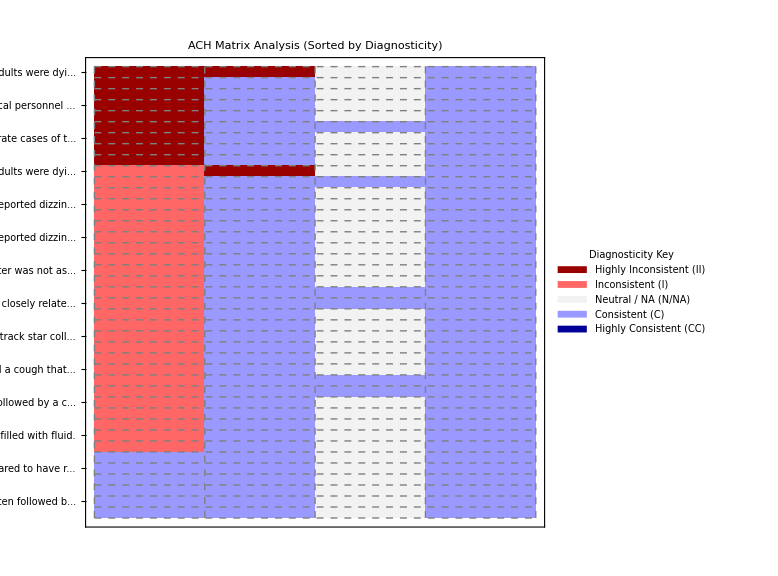

✅ VISUALIZATION COMPLETE. Plot exported to Vault.

```mathematica
(* ======================================================*)(*03:Visualization and Intelligence Report*)(* ======================================================*)Print["--- Initializing Visualization Engine ---"];

(*1. Import Dynamic AI Data*)
expertMatrix=Import["/Users/Western/Desktop/ThesisCode/Vault/ai_scored_matrix.json","JSON"];
hypothesesList=DeleteCases[StringTrim[StringSplit[Import["/Users/Western/Desktop/ThesisCode/Vault/target_hypotheses.md","Text"],"\n"]],""];
rawEvidence=DeleteCases[StringTrim[StringSplit[Import["/Users/Western/Desktop/ThesisCode/Vault/evidence_vault.md","Text"],"\n"]],""];

(*1.5 The Aesthetic Fix:Prepend the E-labels and brutally truncate to fit AspectRatio->1*)
evidenceLabels=MapIndexed["E"<>ToString[#2[[1]]]<>": "<>If[StringLength[#1]>30,StringTake[#1,30]<>"...",#1]&,rawEvidence];

(*2. The Math& Visualization Mapping*)
mathMap={"II"->-2,"I"->-1,"C"->0,"CC"->0,"N"->0,"NA"->0};
numericMatrix=expertMatrix/. mathMap;
hypothesisScores=Total[numericMatrix]; (*Calculates the column sums!*)

visMap={"II"->-2,"I"->-1,"N"->0,"NA"->0,"C"->1,"CC"->2};
visMatrix=expertMatrix/. visMap;

(* ======================================================*)
(*THE UPGRADE:Sort by Diagnosticity!*)
(* ======================================================*)
rowVariances=Variance/@numericMatrix;
sortOrder=Reverse[Ordering[rowVariances]];
sortedVisMatrix=visMatrix[[sortOrder]];
sortedEvidenceLabels=evidenceLabels[[sortOrder]];

(*3. Generate the Upgraded Heatmap (OLD VISUALS)*)
Print["\n--- Generating ACH MatrixPlot ---"];

achPlot=MatrixPlot[sortedVisMatrix,ColorRules->{-2->Darker[Red,0.4],-1->Lighter[Red,0.4],0->Lighter[Gray,0.9],1->Lighter[Blue,0.6],2->Darker[Blue,0.4]},FrameTicks->{(*Left Axis:Evidence (Sorted and Truncated for Safety)*){MapIndexed[{#2[[1]],Style[#1,10,FontFamily->"Helvetica"]}&,sortedEvidenceLabels],None},(*Top Axis:Hypotheses AND Scores! Stacked in a Column inside the Pane*){None,MapIndexed[{#2[[1]],Pane[Column[{Style[#1,10,FontFamily->"Helvetica",Bold],Style["Score: "<>ToString[hypothesisScores[[#2[[1]]]]],10,FontFamily->"Helvetica",FontColor->Darker[Red,0.2],Bold]},Alignment->Center],80,Alignment->Center]}&,hypothesesList]}},FrameTicksStyle->Directive[FontFamily->"Helvetica",10],(*Reverting to the classic dashed mesh*)Mesh->True,MeshStyle->Directive[GrayLevel[0.5],Dashed],PlotLabel->Style["ACH Matrix Analysis (Sorted by Diagnosticity)",Bold,16,FontFamily->"Helvetica"],PlotLegends->Placed[SwatchLegend[{Darker[Red,0.4],Lighter[Red,0.4],Lighter[Gray,0.9],Lighter[Blue,0.6],Darker[Blue,0.4]},{"Highly Inconsistent (II)","Inconsistent (I)","Neutral / NA (N/NA)","Consistent (C)","Highly Consistent (CC)"},LegendLabel->Style["Diagnosticity Key",Bold,12,FontFamily->"Helvetica"],LabelStyle->Directive[FontFamily->"Helvetica",10]],Right],(*Reverting to your exact,stable dimensional code*)ImageSize->Large,AspectRatio->1];

Print[achPlot];

(*4. Export the Visuals*)
exportPath="/Users/Western/Desktop/ThesisCode/Vault/ACH_Final_Heatmap.pdf";
Export[exportPath,achPlot];
Print["\n✅ VISUALIZATION COMPLETE. Plot exported to Vault."];
```